## Fresnel equations:

Given optical constants n and k:

```mathematica
γ = π/2 - β;
a = (n Cos[γ]-1)^2+k^2 Cos[γ]^2;
b = (n Cos[γ]+1)^2+k^2 Cos[γ]^2;
Rp = a/b;
c=(n-Cos[γ])^2+k^2;
Rs = c/d;
```

Simplified formula:

```mathematica
n=14.8; k=15.5;
Ap[θ_]:= 4 n Cos[θ]/((n^2+k^2)Cos[θ]^2+2 n Cos[θ] + 1);
As[θ_]:= 4 n Cos[θ]/((n^2+k^2)+Cos[θ]^2+2 n Cos[θ]);
```

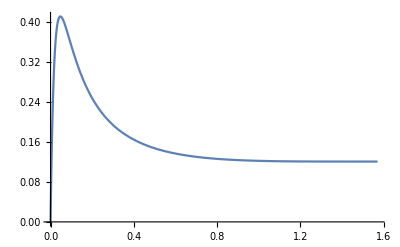

```mathematica
Plot[0.5(As[π/2-θ]+Ap[π/2-θ]),{θ,π/2,0}, PlotRange->All]
```